# Analitični izračuni metamateriala

## zasnova ROC

## Togosti

#### Pozitivna togost

```mathematica
kp=20.372 (Ep I1)/l1^3;
```

#### Negativna togost

```mathematica
(*Pozicije*)
dzg=0.16h;
dsr=1.33 h; 
dsp=1.92h;
dk=1.99h;
(*Negativna togost*)
kn1=9250 (En I2)/l2^3;
kn2=-1253.18 (En I2)/l2^3;
kn3=10571.42 (En I2)/l2^3;
```

### Reševanje pogojne enačbe

```mathematica
(*za Q==6, t1=0.5 in t2=0.25*)
Clear[l1, l2]
Ep = En;
I1=(b t1^3)/12;
I2=(b t2^3)/12;
t1=0.5;
t2=0.25;
r=NSolve[2 kn2 + 4 kp==0 ,{l2}];
l2=l2/.r[[3]]
```

1.56658 l1

### Izbira parametrov

```mathematica
Clear[Ep, En]
Ep=2400(*MPa*);
En=2080(*MPa*);
t1=0.5(*mm*);
t2=0.25(*mm*);
h=10*t2(*mm*);
b=4.0(*mm*);
I1=(b t1^3)/12;
I2=(b t2^3)/12;
l1=13(*mm*);
l2=l2(*mm*);
Print["E_p=",Ep,"MPa, E_n=",En,"MPa, t_1=", t1,"mm, t_2=", t2,"mm, h=", h,"mm, b=", b,"mm, l_1=", l1,"mm, l_2=", l2, "mm"]
```

E_p=2400MPa, E_n=2080MPa, t_1=0.5mm, t_2=0.25mm, h=2.5mm, b=4.mm, l_1=13mm, l_2=20.3656mm

upoštevaj: ω(x)=h/2(1-cos(2π x/l_2))

### Skupna togost in sila ROC

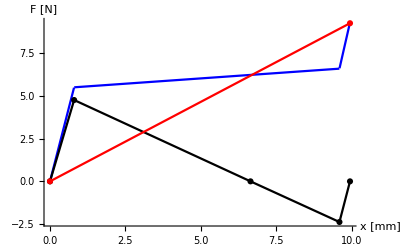

```mathematica
(*Nastavitev vrednosti*)
I1=(b t1^3)/12;
I2=(b t2^3)/12;
kp=20.372 (Ep I1)/l1^3;
kn1=9250 (En I2)/l2^3;
kn2=-1253.18 (En I2)/l2^3;
kn3=10571.42 (En I2)/l2^3;
(*Togost celotne ROC*)
k1=kp+1/2*kn1;
k2=kp+1/2*kn2;
k3=kp+1/2*kn3;
dzg=2*0.16h;
dsr=2*1.33 h; 
dsp=2*1.92h;
dk=2*1.99h;

(*Negativna sila*)
Fzg=1480 (En I2 h)/l2^3;
Fsp=-740 (En I2 h)/l2^3;
(*izris sil*)
p1=ListLinePlot[{{0,0},{dzg,Fzg},{dsr,0},{dsp,Fsp},{dk,0}},PlotMarkers->Automatic,PlotRange->All, PlotStyle-> Black, AxesLabel->{"x [mm]","F [N]"}];
p2=ListLinePlot[{{0,0},{dk,kp*dk}},PlotMarkers->Automatic,PlotRange->All,PlotStyle-> Red, AxesLabel->{"x [mm]","F [N]"}];
(*Sila ROC*)
F1[X_]=k1 X;
F2[X_]=F1[dzg]+k2 (X-dzg);
F3[X_]=F2[dsp]+k3 (X-dsp);
p3=Plot[Piecewise[{
{F1[X],0≤X<dzg},
{F2[X],dzg≤X<dsp},
{F3[X],dsp≤X<dk}
}],{X,0,dk},PlotRange->All, AxesLabel->{"x [mm]","F [N]"},PlotStyle-> Blue];
Show[p3,p1,p2]
```

### (Izpeljava)

```mathematica
(*Določanje μ ub γ*)
D[x-1/2 μ (1/(√(γ^2+x^2))-1)x,x]//Simplify
```

1/2 (2+μ-(γ^2 μ)/((x^2+γ^2)^(3/2)))

```mathematica
Clear[μ, γ]
kroc[x_]=1+1/2 μ-(μ γ^2)/(2(γ^2+x^2)^(3/2));
Simplify[Solve[kroc[0]==υ, μ],{γ>0}]
Simplify[Solve[kroc[0]==υ, γ],{μ>0 }]
```

{{μ→(2 γ (-1+υ))/(-1+γ)}}

{{γ→-μ/(2+μ-2 υ)},{γ→μ/(2+μ-2 υ)}}

```mathematica
(*sila po Taylorju*)
Clear[υ,μ,γ]
fROC[x_]=x-1/2 μ(1/(√(γ^2+x^2))-1)x;
μ=(2 γ (-1+υ))/(-1+γ);
Simplify[Series[fROC[x],{x,0,5}],Assumptions->γ>0]
```

υ x+((-1+υ) x^3)/(2 (-1+γ) γ^2)-(3 (-1+υ) x^5)/(8 ((-1+γ) γ^4))+O[x]^6

### F_ROC(x)

```mathematica
n0=6.25;
γ=0.5;
μ=(2γ)/(1-γ);
a3 = (F2[dsp]-F2[dzg])/(dsp-dzg);
a1=(-1+a3)/(2 (-1+γ) γ^2);
a2=-(3 (-1+a3))/(8 ((-1+γ) γ^4));
fapr[x_]=a3 x + a1 x^3 +a2 x^5;
kapr[x_]=fapr'[x];
Plot[fapr[X],{X,-0.2,0.2},PlotRange->{Automatic,Automatic}, AxesLabel->{"x [mm]","F [N]"}];
Plot[kapr[X],{X,-0.2,0.2},PlotRange->{Automatic,Automatic}, AxesLabel->{"x [mm]","F [N]"}];
```

0.123635+220 (0.000673048 (-4.975+x)^2-5.38438×10^-6 (-4.975+x)^4)

X0 = 4.975 mm

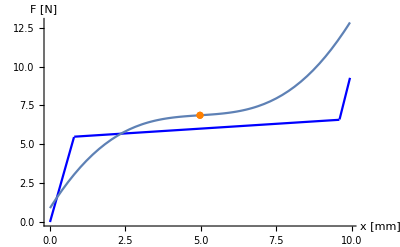

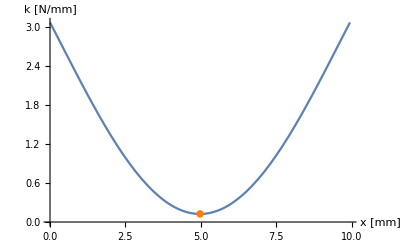

```mathematica
b1=220;
b2=0.04;
Fapr[X_]=n0+a3 X + b1(a1 (b2 (X-dk/2))^3+a2 (b2 (X-dk/2))^5);
k[x_]=Fapr'[x]
(*Iskanje X0 iz sile*)
X0=Solve[Fapr''[x]==0,x][[2,All,2]][[1]];
p4=Plot[Fapr[X],{X,0,dk},PlotRange->{{0,dk},Automatic}, AxesLabel->{"x [mm]","F [N]"}];
p5=Plot[k[X],{X,0,dk},PlotRange->{{0,dk},Automatic}, AxesLabel->{"x [mm]","k [N/mm]"}];
Print["X0 = ",X0, " mm"]
Show[p3,p4,ListPlot[{{X0,Fapr[X0]}},PlotStyle->Orange]]
Show[p5,ListPlot[{{X0,k[X0]}},PlotStyle->Orange]]
```

## Dinamska analiza periodične verige

### Izpeljava po metodi balanc (repeticija članka)

```mathematica
(*Izpeljava izraza za uj(t)*)
q[t_]:=A E^(I Ω t)+B E^(-I Ω t);
u''[t_]:=-q''[t]-2ζ κ q'[t]-κ^2(q[t]+γ q[t]^3);
Collect[u[t]=Integrate[Integrate[u''[t],t],t]//FullSimplify//Expand,E^(-I Ω t)]
```

ⅇ^(ⅈ t Ω) (-A+(A κ^2)/Ω^2+(3 A^2 B γ κ^2)/Ω^2+(2 ⅈ A ζ κ)/Ω)+ⅇ^(-ⅈ t Ω) (-B+(B κ^2)/Ω^2+(3 A B^2 γ κ^2)/Ω^2-(2 ⅈ B ζ κ)/Ω)+(B^3 ⅇ^(-3 ⅈ t Ω) γ κ^2)/(9 Ω^2)+(A^3 ⅇ^(3 ⅈ t Ω) γ κ^2)/(9 Ω^2)

```mathematica
(*izpeljava koeficientov*)
q2[t_]:=A2 ⅇ^(ⅈ t Ω)+B2 ⅇ^(-ⅈ t Ω);
u1[t_]:=(-A1+(A1 κ^2)/Ω^2+(3 A1^2 B1 γ κ^2)/Ω^2+(2 ⅈ A1 ζ κ)/Ω)ⅇ^(ⅈ t Ω)ⅇ^(-ⅈ μ) +(-B1+(B1 κ^2)/Ω^2+(3 A1 B1^2 γ κ^2)/Ω^2-(2 ⅈ B1 ζ κ)/Ω)ⅇ^(-ⅈ t Ω)ⅇ^(-ⅈ μ);
u2[t_]:=(-A2+(A2 κ^2)/Ω^2+(3 A2^2 B2 γ κ^2)/Ω^2+(2 ⅈ A2 ζ κ)/Ω)ⅇ^(ⅈ t Ω)+(-B2+(B2 κ^2)/Ω^2+(3 A2 B2^2 γ κ^2)/Ω^2-(2 ⅈ B2 ζ κ)/Ω);
u3[t_]:=(-A3+(A3 κ^2)/Ω^2+(3 A3^2 B3 γ κ^2)/Ω^2+(2 ⅈ A3 ζ κ)/Ω)ⅇ^(ⅈ t Ω)ⅇ^(ⅈ μ)+(-B3+(B3 κ^2)/Ω^2+(3 A3 B3^2 γ κ^2)/Ω^2-(2 ⅈ B3 ζ κ)/Ω)ⅇ^(-ⅈ t Ω)ⅇ^(ⅈ μ);
Collect[u2''[t]+2u2[t]-u1[t]-u3[t]-2ζ β κ q2'[t]-β κ^2(q2[t]+γ q2[t]^3)//FullSimplify//Expand,E^(I Ω t)]
```

-2 B-B^3 ⅇ^(-3 ⅈ t Ω) β γ κ^2-A^3 ⅇ^(3 ⅈ t Ω) β γ κ^2+(2 B κ^2)/Ω^2+(6 A B^2 γ κ^2)/Ω^2-(4 ⅈ B ζ κ)/Ω+ⅇ^(-ⅈ t Ω) (B ⅇ^(-ⅈ μ)+B ⅇ^(ⅈ μ)-B β κ^2-3 A B^2 β γ κ^2-(B ⅇ^(-ⅈ μ) κ^2)/Ω^2-(B ⅇ^(ⅈ μ) κ^2)/Ω^2-(3 A B^2 ⅇ^(-ⅈ μ) γ κ^2)/Ω^2-(3 A B^2 ⅇ^(ⅈ μ) γ κ^2)/Ω^2+(2 ⅈ B ⅇ^(-ⅈ μ) ζ κ)/Ω+(2 ⅈ B ⅇ^(ⅈ μ) ζ κ)/Ω+2 ⅈ B β ζ κ Ω)+ⅇ^(ⅈ t Ω) (-2 A+A ⅇ^(-ⅈ μ)+A ⅇ^(ⅈ μ)-A κ^2-A β κ^2-3 A^2 B γ κ^2-3 A^2 B β γ κ^2+(2 A κ^2)/Ω^2-(A ⅇ^(-ⅈ μ) κ^2)/Ω^2-(A ⅇ^(ⅈ μ) κ^2)/Ω^2+(6 A^2 B γ κ^2)/Ω^2-(3 A^2 B ⅇ^(-ⅈ μ) γ κ^2)/Ω^2-(3 A^2 B ⅇ^(ⅈ μ) γ κ^2)/Ω^2+(4 ⅈ A ζ κ)/Ω-(2 ⅈ A ⅇ^(-ⅈ μ) ζ κ)/Ω-(2 ⅈ A ⅇ^(ⅈ μ) ζ κ)/Ω-2 ⅈ A ζ κ Ω-2 ⅈ A β ζ κ Ω+A Ω^2)

```mathematica
(*Pogojna enčba μ*)
en[μ_]:=(-2 A+A ⅇ^(-ⅈ μ)+A ⅇ^(ⅈ μ)-A κ^2-A β κ^2-3 A^2 B γ κ^2-3 A^2 B β γ κ^2+(2 A κ^2)/Ω^2-(A ⅇ^(-ⅈ μ) κ^2)/Ω^2-(A ⅇ^(ⅈ μ) κ^2)/Ω^2+(6 A^2 B γ κ^2)/Ω^2-(3 A^2 B ⅇ^(-ⅈ μ) γ κ^2)/Ω^2-(3 A^2 B ⅇ^(ⅈ μ) γ κ^2)/Ω^2+(4 ⅈ A ζ κ)/Ω-(2 ⅈ A ⅇ^(-ⅈ μ) ζ κ)/Ω-(2 ⅈ A ⅇ^(ⅈ μ) ζ κ)/Ω-2 ⅈ A ζ κ Ω-2 ⅈ A β ζ κ Ω+A Ω^2)//FullSimplify
A3=A2=A1=A;
B3=B2=B1=B;
Collect[en[μ],ⅇ^(ⅈ μ)]
```

A (-2+Ω^2+2 Cos[μ]-((1+3 A B γ) κ^2 (-2+(1+β) Ω^2+2 Cos[μ]))/Ω^2-(2 ⅈ ζ κ (-2+(1+β) Ω^2+2 Cos[μ]))/Ω)

```mathematica
Solve[en[μ]==0,Cos[μ]]//FullSimplify
```

{{Cos[μ]→(Ω^2 (-2+Ω^2)-(1+3 A B γ) κ^2 (-2+(1+β) Ω^2)-2 ⅈ ζ κ Ω (-2+(1+β) Ω^2))/((2+6 A B γ) κ^2+4 ⅈ ζ κ Ω-2 Ω^2)}}

```mathematica
(*Numerični test*)
enR[μ]:=(Ω^2 (-2+Ω^2)-(1+3 A B γ) κ^2 (-2+(1+β) Ω^2)-2 ⅈ ζ κ Ω (-2+(1+β) Ω^2))/((2+6 A B γ) κ^2+4 ⅈ ζ κ Ω-2 Ω^2);
enT[μ]:=1-Ω^2/2-1/2(Ω^2 β(κ^2+2 I ζ κ Ω+3 κ^2 γ A B))/(κ^2+2 I ζ κ Ω+3 κ^2 γ A B-Ω^2);
A=21;
B=142;
Ω=123;
β=412;
κ=123;
γ=5123;
ζ=31;

enR[μ]==enT[μ]
```

True

### Izpeljava po metodi balanc lastnega primera

#### Izpeljava (υ=0)

```mathematica
(*Izpeljava izraza za uj(t)*)
q[t_]:=A E^(I Ω t)+B E^(-I Ω t);
u''[t_]:=-q''[t]-2ζ κ q'[t]-κ^2(δ q[t]^3+η q[t]^5);
Collect[u[t_]=Integrate[Integrate[u''[t],t],t]//FullSimplify//Expand,E^(-I Ω t)]
```

ⅇ^(3 ⅈ t Ω) ((A^3 δ κ^2)/(9 Ω^2)+(5 A^4 B η κ^2)/(9 Ω^2))+ⅇ^(-3 ⅈ t Ω) ((B^3 δ κ^2)/(9 Ω^2)+(5 A B^4 η κ^2)/(9 Ω^2))+ⅇ^(ⅈ t Ω) (-A+(3 A^2 B δ κ^2)/Ω^2+(10 A^3 B^2 η κ^2)/Ω^2+(2 ⅈ A ζ κ)/Ω)+ⅇ^(-ⅈ t Ω) (-B+(3 A B^2 δ κ^2)/Ω^2+(10 A^2 B^3 η κ^2)/Ω^2-(2 ⅈ B ζ κ)/Ω)+(B^5 ⅇ^(-5 ⅈ t Ω) η κ^2)/(25 Ω^2)+(A^5 ⅇ^(5 ⅈ t Ω) η κ^2)/(25 Ω^2)

```mathematica
(*izpeljava koeficientov 1*)
q2[t_]=A2 E^(I Ω t)+B2 E^(-I Ω t);
u1[t_]=(-A1+(3 A1^2 B1 δ κ^2)/Ω^2+(10 A1^3 B1^2 η κ^2)/Ω^2+(2 ⅈ A1 ζ κ)/Ω)ⅇ^(ⅈ t Ω)+(-B+(3 A1 B1^2 δ κ^2)/Ω^2+(10 A1^2 B1^3 η κ^2)/Ω^2-(2 ⅈ B1 ζ κ)/Ω)ⅇ^(-ⅈ t Ω) ;
u2[t_]=(-A2+(3 A2^2 B2 δ κ^2)/Ω^2+(10 A2^3 B2^2 η κ^2)/Ω^2+(2 ⅈ A2 ζ κ)/Ω)ⅇ^(ⅈ t Ω)+(-B2+(3 A2 B2^2 δ κ^2)/Ω^2+(10 A2^2 B2^3 η κ^2)/Ω^2-(2 ⅈ B2 ζ κ)/Ω)ⅇ^(-ⅈ t Ω) ;
u3[t_]=(-A3+(3 A3^2 B3 δ κ^2)/Ω^2+(10 A3^3 B3^2 η κ^2)/Ω^2+(2 ⅈ A3 ζ κ)/Ω)ⅇ^(ⅈ t Ω)+(-B3+(3 A3 B3^2 δ κ^2)/Ω^2+(10 A3^2 B3^3 η κ^2)/Ω^2-(2 ⅈ B3 ζ κ)/Ω)ⅇ^(-ⅈ t Ω);
Collect[u2''[t]+2u2[t]-u1[t]-u3[t]-2ζ β κ q2'[t]-α(δ q2[t]^3+η q2[t]^5)//FullSimplify//Expand,E^(I Ω t)]
```

-B2^5 ⅇ^(-5 ⅈ t Ω) α η-A2^5 ⅇ^(5 ⅈ t Ω) α η+ⅇ^(3 ⅈ t Ω) (-A2^3 α δ-5 A2^4 B2 α η)+ⅇ^(-3 ⅈ t Ω) (-B2^3 α δ-5 A2 B2^4 α η)+ⅇ^(ⅈ t Ω) (A1-2 A2+A3-3 A2^2 B2 α δ-10 A2^3 B2^2 α η-3 A2^2 B2 δ κ^2-10 A2^3 B2^2 η κ^2-(3 A1^2 B1 δ κ^2)/Ω^2+(6 A2^2 B2 δ κ^2)/Ω^2-(3 A3^2 B3 δ κ^2)/Ω^2-(10 A1^3 B1^2 η κ^2)/Ω^2+(20 A2^3 B2^2 η κ^2)/Ω^2-(10 A3^3 B3^2 η κ^2)/Ω^2-(2 ⅈ A1 ζ κ)/Ω+(4 ⅈ A2 ζ κ)/Ω-(2 ⅈ A3 ζ κ)/Ω-2 ⅈ A2 ζ κ Ω-2 ⅈ A2 β ζ κ Ω+A2 Ω^2)+ⅇ^(-ⅈ t Ω) (B-2 B2+B3-3 A2 B2^2 α δ-10 A2^2 B2^3 α η-3 A2 B2^2 δ κ^2-10 A2^2 B2^3 η κ^2-(3 A1 B1^2 δ κ^2)/Ω^2+(6 A2 B2^2 δ κ^2)/Ω^2-(3 A3 B3^2 δ κ^2)/Ω^2-(10 A1^2 B1^3 η κ^2)/Ω^2+(20 A2^2 B2^3 η κ^2)/Ω^2-(10 A3^2 B3^3 η κ^2)/Ω^2+(2 ⅈ B1 ζ κ)/Ω-(4 ⅈ B2 ζ κ)/Ω+(2 ⅈ B3 ζ κ)/Ω+2 ⅈ B2 ζ κ Ω+2 ⅈ B2 β ζ κ Ω+B2 Ω^2)

```mathematica
(*izpeljava koeficientov 2*)
q2[t_]=A2 E^(I Ω t)+B2 E^(-I Ω t);
u1[t_]=(-A1+(3 A1^2 B1 δ κ^2)/Ω^2+(10 A1^3 B1^2 η κ^2)/Ω^2+(2 ⅈ A1 ζ κ)/Ω)ⅇ^(ⅈ t Ω)ⅇ^(-ⅈ μ)+(-B+(3 A1 B1^2 δ κ^2)/Ω^2+(10 A1^2 B1^3 η κ^2)/Ω^2-(2 ⅈ B1 ζ κ)/Ω)ⅇ^(-ⅈ t Ω) ⅇ^(-ⅈ μ);
u2[t_]=(-A2+(3 A2^2 B2 δ κ^2)/Ω^2+(10 A2^3 B2^2 η κ^2)/Ω^2+(2 ⅈ A2 ζ κ)/Ω)ⅇ^(ⅈ t Ω)+(-B2+(3 A2 B2^2 δ κ^2)/Ω^2+(10 A2^2 B2^3 η κ^2)/Ω^2-(2 ⅈ B2 ζ κ)/Ω)ⅇ^(-ⅈ t Ω) ;
u3[t_]=(-A3+(3 A3^2 B3 δ κ^2)/Ω^2+(10 A3^3 B3^2 η κ^2)/Ω^2+(2 ⅈ A3 ζ κ)/Ω)ⅇ^(ⅈ t Ω)ⅇ^(+ⅈ μ)+(-B3+(3 A3 B3^2 δ κ^2)/Ω^2+(10 A3^2 B3^3 η κ^2)/Ω^2-(2 ⅈ B3 ζ κ)/Ω)ⅇ^(-ⅈ t Ω)ⅇ^(+ⅈ μ) ;
```

```mathematica
Collect[u2''[t]+2u2[t]-u1[t]-u3[t]-2ζ β κ q2'[t]-α(δ q2[t]^3+η q2[t]^5)//FullSimplify//Expand,E^(I Ω t)]
```

-B2^5 ⅇ^(-5 ⅈ t Ω) α η-A2^5 ⅇ^(5 ⅈ t Ω) α η+ⅇ^(3 ⅈ t Ω) (-A2^3 α δ-5 A2^4 B2 α η)+ⅇ^(-3 ⅈ t Ω) (-B2^3 α δ-5 A2 B2^4 α η)+ⅇ^(ⅈ t Ω) (-2 A2+A1 ⅇ^(-ⅈ μ)+A3 ⅇ^(ⅈ μ)-3 A2^2 B2 α δ-10 A2^3 B2^2 α η-3 A2^2 B2 δ κ^2-10 A2^3 B2^2 η κ^2+(6 A2^2 B2 δ κ^2)/Ω^2-(3 A1^2 B1 ⅇ^(-ⅈ μ) δ κ^2)/Ω^2-(3 A3^2 B3 ⅇ^(ⅈ μ) δ κ^2)/Ω^2+(20 A2^3 B2^2 η κ^2)/Ω^2-(10 A1^3 B1^2 ⅇ^(-ⅈ μ) η κ^2)/Ω^2-(10 A3^3 B3^2 ⅇ^(ⅈ μ) η κ^2)/Ω^2+(4 ⅈ A2 ζ κ)/Ω-(2 ⅈ A1 ⅇ^(-ⅈ μ) ζ κ)/Ω-(2 ⅈ A3 ⅇ^(ⅈ μ) ζ κ)/Ω-2 ⅈ A2 ζ κ Ω-2 ⅈ A2 β ζ κ Ω+A2 Ω^2)+ⅇ^(-ⅈ t Ω) (-2 B2+B ⅇ^(-ⅈ μ)+B3 ⅇ^(ⅈ μ)-3 A2 B2^2 α δ-10 A2^2 B2^3 α η-3 A2 B2^2 δ κ^2-10 A2^2 B2^3 η κ^2+(6 A2 B2^2 δ κ^2)/Ω^2-(3 A1 B1^2 ⅇ^(-ⅈ μ) δ κ^2)/Ω^2-(3 A3 B3^2 ⅇ^(ⅈ μ) δ κ^2)/Ω^2+(20 A2^2 B2^3 η κ^2)/Ω^2-(10 A1^2 B1^3 ⅇ^(-ⅈ μ) η κ^2)/Ω^2-(10 A3^2 B3^3 ⅇ^(ⅈ μ) η κ^2)/Ω^2-(4 ⅈ B2 ζ κ)/Ω+(2 ⅈ B1 ⅇ^(-ⅈ μ) ζ κ)/Ω+(2 ⅈ B3 ⅇ^(ⅈ μ) ζ κ)/Ω+2 ⅈ B2 ζ κ Ω+2 ⅈ B2 β ζ κ Ω+B2 Ω^2)

```mathematica
(*Pogojna enčba μ*)
en[μ_]:=(-2 A2+A1 ⅇ^(-ⅈ μ)+A3 ⅇ^(ⅈ μ)-3 A2^2 B2 α δ-10 A2^3 B2^2 α η-3 A2^2 B2 δ κ^2-10 A2^3 B2^2 η κ^2+(6 A2^2 B2 δ κ^2)/Ω^2-(3 A1^2 B1 ⅇ^(-ⅈ μ) δ κ^2)/Ω^2-(3 A3^2 B3 ⅇ^(ⅈ μ) δ κ^2)/Ω^2+(20 A2^3 B2^2 η κ^2)/Ω^2-(10 A1^3 B1^2 ⅇ^(-ⅈ μ) η κ^2)/Ω^2-(10 A3^3 B3^2 ⅇ^(ⅈ μ) η κ^2)/Ω^2+(4 ⅈ A2 ζ κ)/Ω-(2 ⅈ A1 ⅇ^(-ⅈ μ) ζ κ)/Ω-(2 ⅈ A3 ⅇ^(ⅈ μ) ζ κ)/Ω-2 ⅈ A2 ζ κ Ω-2 ⅈ A2 β ζ κ Ω+A2 Ω^2)//FullSimplify
A3=A2=A1=A;
B3=B2=B1=B;
Collect[en[μ],ⅇ^(ⅈ μ)]
```

-(A (-2 A B (3 δ+10 A B η) κ^2-4 ⅈ ζ κ Ω+(2+A B (3 δ+10 A B η) (α+κ^2)) Ω^2+2 ⅈ (1+β) ζ κ Ω^3-Ω^4+(2 A B (3 δ+10 A B η) κ^2+4 ⅈ ζ κ Ω-2 Ω^2) Cos[μ]))/Ω^2

```mathematica
Solve[en[μ]==0,Cos[μ]]//FullSimplify
```

{{Cos[μ]→(2 A B (3 δ+10 A B η) κ^2+4 ⅈ ζ κ Ω-(2+A B (3 δ+10 A B η) (α+κ^2)) Ω^2-2 ⅈ (1+β) ζ κ Ω^3+Ω^4)/(2 A B (3 δ+10 A B η) κ^2+4 ⅈ ζ κ Ω-2 Ω^2)}}

#### Izpeljava(υ=konst.)

```mathematica
(*Izpeljava izraza za uj(t)*)
Clear[υ]
q[t_]:=A E^(I Ω t)+B E^(-I Ω t);
u''[t_]:=-q''[t]-2ζ κ q'[t]-κ^2(υ q[t]+  δ q[t]^3+η q[t]^5);
Collect[u[t_]=Integrate[Integrate[u''[t],t],t]//FullSimplify//Expand,E^(-I Ω t)]
```

ⅇ^(3 ⅈ t Ω) ((A^3 δ κ^2)/(9 Ω^2)+(5 A^4 B η κ^2)/(9 Ω^2))+ⅇ^(-3 ⅈ t Ω) ((B^3 δ κ^2)/(9 Ω^2)+(5 A B^4 η κ^2)/(9 Ω^2))+ⅇ^(ⅈ t Ω) (-A+(3 A^2 B δ κ^2)/Ω^2+(10 A^3 B^2 η κ^2)/Ω^2+(A κ^2 υ)/Ω^2+(2 ⅈ A ζ κ)/Ω)+ⅇ^(-ⅈ t Ω) (-B+(3 A B^2 δ κ^2)/Ω^2+(10 A^2 B^3 η κ^2)/Ω^2+(B κ^2 υ)/Ω^2-(2 ⅈ B ζ κ)/Ω)+(B^5 ⅇ^(-5 ⅈ t Ω) η κ^2)/(25 Ω^2)+(A^5 ⅇ^(5 ⅈ t Ω) η κ^2)/(25 Ω^2)

```mathematica
(*izpeljava koeficientov 1*)
q2[t_]=A2 E^(I Ω t)+B2 E^(-I Ω t);
u1[t_]=(-A1+(3 A1^2 B1 δ κ^2)/Ω^2+(10 A1^3 B1^2 η κ^2)/Ω^2+(A1 κ^2 υ)/Ω^2+(2 ⅈ A1 ζ κ)/Ω)ⅇ^(ⅈ t Ω)+(-B1+(3 A1 B1^2 δ κ^2)/Ω^2+(10 A1^2 B1^3 η κ^2)/Ω^2+(B1 κ^2 υ)/Ω^2-(2 ⅈ B1 ζ κ)/Ω)ⅇ^(-ⅈ t Ω) ;
u2[t_]=(-A2+(3 A2^2 B2 δ κ^2)/Ω^2+(10 A2^3 B2^2 η κ^2)/Ω^2+(A2 κ^2 υ)/Ω^2+(2 ⅈ A2 ζ κ)/Ω)ⅇ^(ⅈ t Ω)+(-B2+(3 A2 B2^2 δ κ^2)/Ω^2+(10 A2^2 B2^3 η κ^2)/Ω^2+(B2 κ^2 υ)/Ω^2-(2 ⅈ B2 ζ κ)/Ω)ⅇ^(-ⅈ t Ω) ;
u3[t_]=(-A3+(3 A3^2 B3 δ κ^2)/Ω^2+(10 A3^3 B3^2 η κ^2)/Ω^2+(A3 κ^2 υ)/Ω^2+(2 ⅈ A3 ζ κ)/Ω)ⅇ^(ⅈ t Ω)+(-B3+(3 A3 B3^2 δ κ^2)/Ω^2+(10 A3^2 B3^3 η κ^2)/Ω^2+(B3 κ^2 υ)/Ω^2-(2 ⅈ B3 ζ κ)/Ω)ⅇ^(-ⅈ t Ω) ;
Collect[u2''[t]+2u2[t]-u1[t]-u3[t]-2ζ β κ q2'[t]-α(υ q2[t]+ δ q2[t]^3+η q2[t]^5)//FullSimplify//Expand,E^(I Ω t)]
```

-B2^5 ⅇ^(-5 ⅈ t Ω) α η-A2^5 ⅇ^(5 ⅈ t Ω) α η+ⅇ^(3 ⅈ t Ω) (-A2^3 α δ-5 A2^4 B2 α η)+ⅇ^(-3 ⅈ t Ω) (-B2^3 α δ-5 A2 B2^4 α η)+ⅇ^(ⅈ t Ω) (A1-2 A2+A3-3 A2^2 B2 α δ-10 A2^3 B2^2 α η-3 A2^2 B2 δ κ^2-10 A2^3 B2^2 η κ^2-A2 α υ-A2 κ^2 υ-(3 A1^2 B1 δ κ^2)/Ω^2+(6 A2^2 B2 δ κ^2)/Ω^2-(3 A3^2 B3 δ κ^2)/Ω^2-(10 A1^3 B1^2 η κ^2)/Ω^2+(20 A2^3 B2^2 η κ^2)/Ω^2-(10 A3^3 B3^2 η κ^2)/Ω^2-(A1 κ^2 υ)/Ω^2+(2 A2 κ^2 υ)/Ω^2-(A3 κ^2 υ)/Ω^2-(2 ⅈ A1 ζ κ)/Ω+(4 ⅈ A2 ζ κ)/Ω-(2 ⅈ A3 ζ κ)/Ω-2 ⅈ A2 ζ κ Ω-2 ⅈ A2 β ζ κ Ω+A2 Ω^2)+ⅇ^(-ⅈ t Ω) (B1-2 B2+B3-3 A2 B2^2 α δ-10 A2^2 B2^3 α η-3 A2 B2^2 δ κ^2-10 A2^2 B2^3 η κ^2-B2 α υ-B2 κ^2 υ-(3 A1 B1^2 δ κ^2)/Ω^2+(6 A2 B2^2 δ κ^2)/Ω^2-(3 A3 B3^2 δ κ^2)/Ω^2-(10 A1^2 B1^3 η κ^2)/Ω^2+(20 A2^2 B2^3 η κ^2)/Ω^2-(10 A3^2 B3^3 η κ^2)/Ω^2-(B1 κ^2 υ)/Ω^2+(2 B2 κ^2 υ)/Ω^2-(B3 κ^2 υ)/Ω^2+(2 ⅈ B1 ζ κ)/Ω-(4 ⅈ B2 ζ κ)/Ω+(2 ⅈ B3 ζ κ)/Ω+2 ⅈ B2 ζ κ Ω+2 ⅈ B2 β ζ κ Ω+B2 Ω^2)

```mathematica
(*izpeljava koeficientov 2*)
q2[t_]=A2 E^(I Ω t)+B2 E^(-I Ω t);
u1[t_]=(-A1+(3 A1^2 B1 δ κ^2)/Ω^2+(10 A1^3 B1^2 η κ^2)/Ω^2+(A1 κ^2 υ)/Ω^2+(2 ⅈ A1 ζ κ)/Ω)ⅇ^(ⅈ t Ω)ⅇ^(-ⅈ μ)+(-B1+(3 A1 B1^2 δ κ^2)/Ω^2+(10 A1^2 B1^3 η κ^2)/Ω^2+(B1 κ^2 υ)/Ω^2-(2 ⅈ B1 ζ κ)/Ω)ⅇ^(-ⅈ t Ω) ⅇ^(-ⅈ μ);
u2[t_]=(-A2+(3 A2^2 B2 δ κ^2)/Ω^2+(10 A2^3 B2^2 η κ^2)/Ω^2+(A2 κ^2 υ)/Ω^2+(2 ⅈ A2 ζ κ)/Ω)ⅇ^(ⅈ t Ω)+(-B2+(3 A2 B2^2 δ κ^2)/Ω^2+(10 A2^2 B2^3 η κ^2)/Ω^2+(B2 κ^2 υ)/Ω^2-(2 ⅈ B2 ζ κ)/Ω)ⅇ^(-ⅈ t Ω) ;
u3[t_]=(-A3+(3 A3^2 B3 δ κ^2)/Ω^2+(10 A3^3 B3^2 η κ^2)/Ω^2+(A3 κ^2 υ)/Ω^2+(2 ⅈ A3 ζ κ)/Ω)ⅇ^(ⅈ t Ω)ⅇ^(+ⅈ μ)+(-B3+(3 A3 B3^2 δ κ^2)/Ω^2+(10 A3^2 B3^3 η κ^2)/Ω^2+(B3 κ^2 υ)/Ω^2-(2 ⅈ B3 ζ κ)/Ω)ⅇ^(-ⅈ t Ω)ⅇ^(+ⅈ μ) ;
```

```mathematica
Collect[u2''[t]+2u2[t]-u1[t]-u3[t]-2ζ β κ q2'[t]-α(υ q2[t]+ δ q2[t]^3+η q2[t]^5)//FullSimplify//Expand,E^(I Ω t)]
```

-B2^5 ⅇ^(-5 ⅈ t Ω) α η-A2^5 ⅇ^(5 ⅈ t Ω) α η+ⅇ^(3 ⅈ t Ω) (-A2^3 α δ-5 A2^4 B2 α η)+ⅇ^(-3 ⅈ t Ω) (-B2^3 α δ-5 A2 B2^4 α η)+ⅇ^(ⅈ t Ω) (-2 A2+A1 ⅇ^(-ⅈ μ)+A3 ⅇ^(ⅈ μ)-3 A2^2 B2 α δ-10 A2^3 B2^2 α η-3 A2^2 B2 δ κ^2-10 A2^3 B2^2 η κ^2-A2 α υ-A2 κ^2 υ+(6 A2^2 B2 δ κ^2)/Ω^2-(3 A1^2 B1 ⅇ^(-ⅈ μ) δ κ^2)/Ω^2-(3 A3^2 B3 ⅇ^(ⅈ μ) δ κ^2)/Ω^2+(20 A2^3 B2^2 η κ^2)/Ω^2-(10 A1^3 B1^2 ⅇ^(-ⅈ μ) η κ^2)/Ω^2-(10 A3^3 B3^2 ⅇ^(ⅈ μ) η κ^2)/Ω^2+(2 A2 κ^2 υ)/Ω^2-(A1 ⅇ^(-ⅈ μ) κ^2 υ)/Ω^2-(A3 ⅇ^(ⅈ μ) κ^2 υ)/Ω^2+(4 ⅈ A2 ζ κ)/Ω-(2 ⅈ A1 ⅇ^(-ⅈ μ) ζ κ)/Ω-(2 ⅈ A3 ⅇ^(ⅈ μ) ζ κ)/Ω-2 ⅈ A2 ζ κ Ω-2 ⅈ A2 β ζ κ Ω+A2 Ω^2)+ⅇ^(-ⅈ t Ω) (-2 B2+B1 ⅇ^(-ⅈ μ)+B3 ⅇ^(ⅈ μ)-3 A2 B2^2 α δ-10 A2^2 B2^3 α η-3 A2 B2^2 δ κ^2-10 A2^2 B2^3 η κ^2-B2 α υ-B2 κ^2 υ+(6 A2 B2^2 δ κ^2)/Ω^2-(3 A1 B1^2 ⅇ^(-ⅈ μ) δ κ^2)/Ω^2-(3 A3 B3^2 ⅇ^(ⅈ μ) δ κ^2)/Ω^2+(20 A2^2 B2^3 η κ^2)/Ω^2-(10 A1^2 B1^3 ⅇ^(-ⅈ μ) η κ^2)/Ω^2-(10 A3^2 B3^3 ⅇ^(ⅈ μ) η κ^2)/Ω^2+(2 B2 κ^2 υ)/Ω^2-(B1 ⅇ^(-ⅈ μ) κ^2 υ)/Ω^2-(B3 ⅇ^(ⅈ μ) κ^2 υ)/Ω^2-(4 ⅈ B2 ζ κ)/Ω+(2 ⅈ B1 ⅇ^(-ⅈ μ) ζ κ)/Ω+(2 ⅈ B3 ⅇ^(ⅈ μ) ζ κ)/Ω+2 ⅈ B2 ζ κ Ω+2 ⅈ B2 β ζ κ Ω+B2 Ω^2)

```mathematica
(*Pogojna enčba μ*)
en[μ_]:=(-2 A2+A1 ⅇ^(-ⅈ μ)+A3 ⅇ^(ⅈ μ)-3 A2^2 B2 α δ-10 A2^3 B2^2 α η-3 A2^2 B2 δ κ^2-10 A2^3 B2^2 η κ^2-A2 α υ-A2 κ^2 υ+(6 A2^2 B2 δ κ^2)/Ω^2-(3 A1^2 B1 ⅇ^(-ⅈ μ) δ κ^2)/Ω^2-(3 A3^2 B3 ⅇ^(ⅈ μ) δ κ^2)/Ω^2+(20 A2^3 B2^2 η κ^2)/Ω^2-(10 A1^3 B1^2 ⅇ^(-ⅈ μ) η κ^2)/Ω^2-(10 A3^3 B3^2 ⅇ^(ⅈ μ) η κ^2)/Ω^2+(2 A2 κ^2 υ)/Ω^2-(A1 ⅇ^(-ⅈ μ) κ^2 υ)/Ω^2-(A3 ⅇ^(ⅈ μ) κ^2 υ)/Ω^2+(4 ⅈ A2 ζ κ)/Ω-(2 ⅈ A1 ⅇ^(-ⅈ μ) ζ κ)/Ω-(2 ⅈ A3 ⅇ^(ⅈ μ) ζ κ)/Ω-2 ⅈ A2 ζ κ Ω-2 ⅈ A2 β ζ κ Ω+A2 Ω^2)//FullSimplify
A3=A2=A1=A;
B3=B2=B1=B;
Collect[en[μ],ⅇ^(ⅈ μ)]
```

(A (2 κ^2 (A B (3 δ+10 A B η)+υ)+4 ⅈ ζ κ Ω-(2+(α+κ^2) (A B (3 δ+10 A B η)+υ)) Ω^2-2 ⅈ (1+β) ζ κ Ω^3+Ω^4-2 (κ^2 (A B (3 δ+10 A B η)+υ)+2 ⅈ ζ κ Ω-Ω^2) Cos[μ]))/Ω^2

```mathematica
Solve[en[μ]==0,Cos[μ]]//FullSimplify
```

{{Cos[μ]→(2 κ^2 (A B (3 δ+10 A B η)+υ)+4 ⅈ ζ κ Ω-(2+(α+κ^2) (A B (3 δ+10 A B η)+υ)) Ω^2-2 ⅈ (1+β) ζ κ Ω^3+Ω^4)/(2 κ^2 (A B (3 δ+10 A B η)+υ)+4 ⅈ ζ κ Ω-2 Ω^2)}}

#### Izris

```mathematica
(*Končna funkcija*)
μu[Ω_]:=ArcCos[(2 κ^2 (A B (3 δ+10 A B η)+υ)+4 ⅈ ζ κ Ω-(2+(α+κ^2) (A B (3 δ+10 A B η)+υ)) Ω^2-2 ⅈ (1+β) ζ κ Ω^3+Ω^4)/(2 κ^2 (A B (3 δ+10 A B η)+υ)+4 ⅈ ζ κ Ω-2 Ω^2)]
```

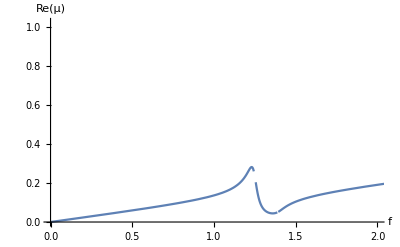

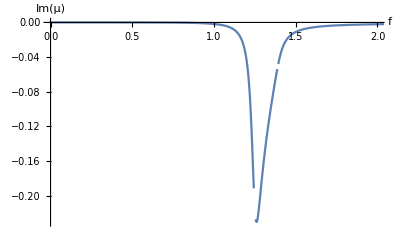

```mathematica
(*amplitude*) 
AB=0.01;
A = 1;
B=AB/A(*amplituda mase m*);
(*mase*)
m=0.44 10^-3;
M=1.72 10^-3;
β=m/M;
(*togosti*)
t3 = 0.75;
l3 = 13;
I3 = b t3^3 / 12;
K=2*(20.372*Ep*I3/l3^3);
k=a3;
α=k/K;
(*dušenje*)
ζ=0.01;
(*lastne frekvence*)
ω0=√(K/M);
κ=√(α/β);
Ω[f_]=2π f/ω0(*ω/ω0*);
(*funkcija*)
υ=a3;
δ=a1;
η=a2;

Plot[Re[μu[Ω[f]]],{f,0,3π},AxesLabel->{"f","Re(μ)"}, PlotRange->{{0,2},Full}]
Plot[Im[μu[Ω[f]]],{f,0,3π},AxesLabel->{"f","Im(μ)"}, PlotRange->{{0,2},Full}]
```

## Končna veriga

```mathematica
(*skupni podatki*)
m=0.44 10^-6(*ton - masa resonatorja*);
M=1.72 10^-6(*ton - masa ROC*);
g=9.806 10^-3(*gravitacija*);
β=m/M;
ζ=0.01*(3 β)/(8(1+β)^3);
c=2m √(K/M) ζ(*faktor dušenja*);
t3 = 0.75(*mm*);
l3 = l1(*mm*);
I3 = b t3^3 / 12;
K=2*(20.372*Ep*I3/l3^3)(*vmesna togost*);
(*št. ROC*)
n=3;
(*frekvenca*)
fmax=1000(*max frekvenca*);
fmin=0.1(*min frekvenca*);
kfr=1(*korak frekvence*);
(*bandgap*)
fmaxgap=100(*max frekvenca*);
fmingap=50(*min frekvenca*);
kfrgap=0.1(*korak frekvence*);
```

### n ROC (linearizirano)

```mathematica
k0=k[X0];
(*Masna matrika*)
Ms=Table[0,{i,1,2n},{j,1,2n}];
For[i=1,i≤2n,i++,
For[j=1,j≤ 2n,j++,
If[Mod[i,2]==1 && i==j,Ms[[i,j]]=M];
If[Mod[i,2]==0 && i==j,Ms[[i,j]]=m];
If[Mod[i,2]==0 && i==j+1,Ms[[i,j]]=m];
];]
(*Togostna Matrika*)
Ks=Table[0,{i,1,2n},{j,1,2n}];
p=0;
For[i=1,i≤2n,i++,
For[j=1,j≤ 2n,j++,
If[Mod[i,2]==1 && i==j,p+=1];
If[Mod[i,2]==1 && i==j,Ks[[i,j]]=2K];
If[Mod[i,2]==1 && i==j-2,Ks[[i,j]]=-K];
If[Mod[i,2]==1 && i==j+2,Ks[[i,j]]=-K];
If[Mod[i,2]==1 && i==j-1,Ks[[i,j]]=-k0];
If[Mod[i,2]==0 && i==j,Ks[[i,j]]=k0];
];
];
(*Matrika dušenja*)
Ds=Table[0,{i,1,2n},{j,1,2n}];
For[i=1,i≤2n,i++,
For[j=1,j≤ 2n,j++,
If[Mod[i,2]==1 && i==j-1,Ds[[i,j]]=-c];
If[Mod[i,2]==0 && i==j,Ds[[i,j]]=c];
];]
(*Print["Ms U''+ Ds U' + Ks U = F"]
Print[MatrixForm[Ms],"U''","+",MatrixForm[Ds],"U'","+",MatrixForm[Ks],"U","=","F"]*)
```

```mathematica
(*Lastne fekvence*)
Clear[λ]
Solve[Det[Ks.Inverse[Ms]-λ IdentityMatrix[2n]]==0,λ];
λ=λ/.%;
f0=√λ/(2π)
```

{82.782,83.9356,84.117,236.814,431.562,562.647}

```mathematica
(*Matrika FRF*)
Hd[ω_]=Inverse[Ks+I ω Ds-ω^2 Ms];
```

```mathematica
(*Reševanje*)
fi=Range[fmin,fmax,kfr];
ωi=2π fi;
Hin=Table[0,{i,1,Length[ωi]}];
Hout=Table[0,{i,1,Length[ωi]}];
Monitor[
For[i=1,i≤Length[ωi],i++,
Hin[[i]]=Hd[ωi[[i]]][[1,1]];
Hout[[i]]=Hd[ωi[[i]]][[1,-2]];
];
,N[i/Length[ωi]*100,3]]
```

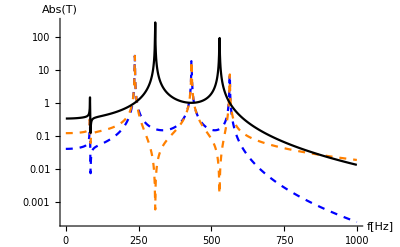

```mathematica
(*Izris*)
gf11=ListLogPlot[Transpose[{fi,Abs[Hout]}],PlotStyle->{Dashed,Blue},Joined->True];
gf12=ListLogPlot[Transpose[{fi,Abs[Hin]}],PlotStyle->{Dashed,Orange},Joined->True];
gf13=ListLogPlot[Transpose[{fi,Abs[Hout/Hin]}],PlotStyle->{Black},Joined->True];
Show[gf11,gf12,gf13,PlotRange->All,AxesLabel->{"f[Hz]","Abs(T)"}]
```

```mathematica
(*Reševanje closeup*)
figap=Range[fmingap,fmaxgap,kfrgap];
ωi=2π figap;
Hingap=Table[0,{i,1,Length[ωi]}];
Houtgap=Table[0,{i,1,Length[ωi]}];
Monitor[
For[i=1,i≤Length[ωi],i++,
Hingap[[i]]=Hd[ωi[[i]]][[1,1]];
Houtgap[[i]]=Hd[ωi[[i]]][[1,-2]];
];
,N[i/Length[ωi]*100,3]]
```

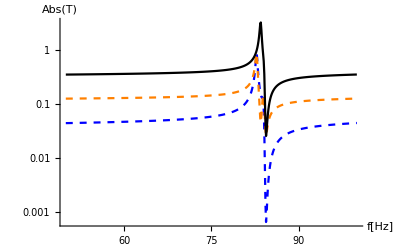

```mathematica
(*Izris*)
gf11gap=ListLogPlot[Transpose[{figap,Abs[Houtgap]}],PlotStyle->{Dashed,Blue},Joined->True];
gf12gap=ListLogPlot[Transpose[{figap,Abs[Hingap]}],PlotStyle->{Dashed,Orange},Joined->True];
gf13gap=ListLogPlot[Transpose[{figap,Abs[Houtgap/Hingap]}],PlotStyle->{Black},Joined->True];
Show[gf11gap,gf12gap,gf13gap,PlotRange->All,AxesLabel->{"f[Hz]","Abs(T)"}]
```

### n ROC (Runge-Kutta)

```mathematica
(*Neznanke*)
Uj[t_]=Table[{Subscript[U, i][t],Subscript[Q, i][t]},{i,1,n}]//Flatten;
(*sila*)
F=Table[0,{i,1,2n}];
F[[1]]=F0 Sin[ω t] ;F0=n(M+m)*g(*N*);
(*Masna matrika*)
Ms=Table[0,{i,1,2n},{j,1,2n}];
For[i=1,i≤2n,i++,
For[j=1,j≤ 2n,j++,
If[Mod[i,2]==1 && i==j,Ms[[i,j]]=M];
If[Mod[i,2]==0 && i==j,Ms[[i,j]]=m];
If[Mod[i,2]==0 && i==j+1,Ms[[i,j]]=m];
];]
(*Togostna Matrika*)
Ks=Table[0,{i,1,2n},{j,1,2n}];
p=0;
For[i=1,i≤2n,i++,
For[j=1,j≤ 2n,j++,
If[Mod[i,2]==1 && i==j,p+=1];
If[Mod[i,2]==1 && i==j,Ks[[i,j]]=2K];
If[Mod[i,2]==1 && i==j-2,Ks[[i,j]]=-K];
If[Mod[i,2]==1 && i==j+2,Ks[[i,j]]=-K];
If[Mod[i,2]==1 && i==j-1,Ks[[i,j]]=-k[X0+Subscript[Q, p][t]]];
If[Mod[i,2]==0 && i==j,Ks[[i,j]]=k[X0+Subscript[Q, p][t]]];
];]
(*Matrika dušenja*)
Ds=Table[0,{i,1,2n},{j,1,2n}];
For[i=1,i≤2n,i++,
For[j=1,j≤ 2n,j++,
If[Mod[i,2]==1 && i==j-1,Ds[[i,j]]=-c];
If[Mod[i,2]==0 && i==j,Ds[[i,j]]=c];
];]
(*Print["Ms U''+ Ds U' + Ks U = F"]
Print[MatrixForm[Ms],MatrixForm[Uj''[t]],"+",MatrixForm[Ds],MatrixForm[Uj'[t]],"+",MatrixForm[Ks],MatrixForm[Uj],"=",MatrixForm[F]]*)
```

#### (Loop test)

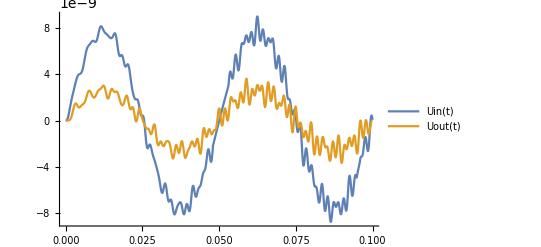

```mathematica
(*FRF*)
tmax=0.1;
tmin=0;
f=20;
sr=2^15(*Sample Rate*);
sol=NDSolve[{
Ms.Uj''[t]+Ks.Uj[t]==F,ω==2π f,
Uj[0]==Table[0,{i,1,2n}], 
Uj'[0]==Table[0,{i,1,2n}]
},Uj[t],{t,0,tmax}];
Usol[t_]=Uj[t]/.sol;
Uin[t_]=Usol[t][[1,1]];
Uout[t_]=Usol[t][[1,-2]];
tData = Table[t,{t,tmin,tmax,1/sr}];
UinData=Table[Uin[t],{t,tmin,tmax,1/sr}];
UoutData=Table[Uout[t],{t,tmin,tmax,1/sr}];
Plot[{Uin[t],Uout[t]},{t,tmin,tmax},PlotRange->All,PlotLegends->"Expressions"]
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\tData.txt",tData,"Table"];Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\UinData.txt",UinData,"Table"];
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\UoutData.txt",UoutData,"Table"];
```

#### FRF

```mathematica
(*Reševanje*)
nfr=(fmax-fmin)/kfr;
tmax=0.3;
tmin=0.1;
sr=2^14(*Sample Rate*);
Clear[ft, ff]
ft={};ff={};
Monitor[
For[i=0,i≤nfr,i++,
sol=NDSolve[{
Ms.Uj''[t]+Ks.Uj[t]==F,ω==2π ( fmin+kfr*i),
Uj[0]==Table[0,{i,1,2n}], 
Uj'[0]==Table[0,{i,1,2n}]
},Uj[t],{t,tmin,tmax}];
Usol[t_]=Uj[t]/.sol;
Uin[t_]=Usol[t][[1,1]];
Uout[t_]=Usol[t][[1,-2]];
UinData=Table[Uin[t],{t,tmin,tmax,1/sr}];
UoutData=Table[Uout[t],{t,tmin,tmax,1/sr}];
ft1=Fourier[UinData];
ft2=Fourier[UoutData];
fti=ft2/ft1;
len=Table[(n-1) sr/Length@fti,{n,Length@fti}];
index=FirstPosition[len,Nearest[len,fmin+kfr*i][[1]]][[1]];
AppendTo[ft,fti[[index]]];
AppendTo[ff,fmin+kfr*i];
]
,N[i/nfr,2]]
```

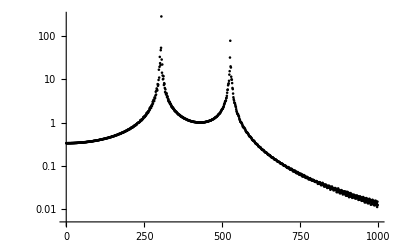

```mathematica
(*Izris*)
gf23=ListLogPlot[Transpose[{ff,Abs[ft]}],PlotStyle->{Black}]
```

```mathematica
(*bandgap*)
(*Reševanje closeup*)
nfr=(fmaxgap-fmingap)/kfrgap;
tmax=0.5;
tmin=0.1;
sr=2^15(*Sample Rate*);
Clear[ftgap, ffgap]
ftgap={};ffgap={};
Monitor[
For[i=0,i≤nfr,i++,
sol=NDSolve[{
Ms.Uj''[t]+Ks.Uj[t]==F,ω==2π ( fmingap+kfrgap*i),
Uj[0]==Table[0,{i,1,2n}], 
Uj'[0]==Table[0,{i,1,2n}]
},Uj[t],{t,tmin,tmax}];
Usol[t_]=Uj[t]/.sol;
Uin[t_]=Usol[t][[1,1]];
Uout[t_]=Usol[t][[1,-2]];
UinData=Table[Uin[t],{t,tmin,tmax,1/sr}];
UoutData=Table[Uout[t],{t,tmin,tmax,1/sr}];
ft1=Fourier[UinData];
ft2=Fourier[UoutData];
fti=ft2/ft1;
len=Table[(n-1) sr/Length@fti,{n,Length@fti}];
index=FirstPosition[len,Nearest[len,fmingap+kfrgap*i][[1]]][[1]];
AppendTo[ftgap,fti[[index]]];
AppendTo[ffgap,fmingap+kfrgap*i];
]
,N[i/nfr*100,2]]
```

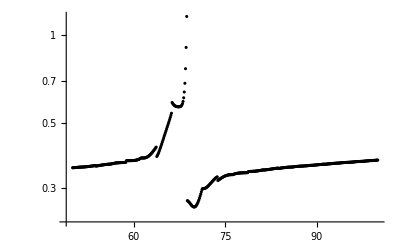

```mathematica
(*Izris*)
gf23gap=ListLogPlot[Transpose[{ffgap,Abs[ftgap]}],PlotRange->All,PlotStyle->{Black}]
```

### Shranjevanje in končni prikaz

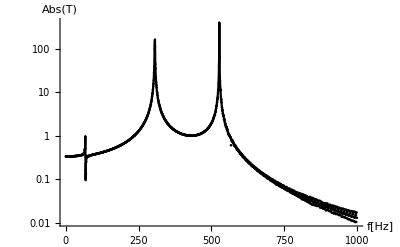

za prednapetje X0=4.975 in št ROC = 3

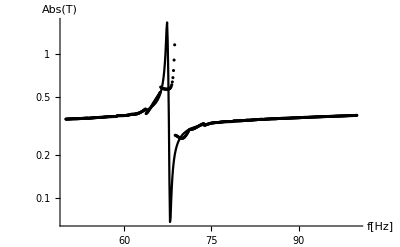

```mathematica
(*FULL*)
(*linearizirano*)
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\Mathematica\\ff_lin.txt",fi,"Table"];
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\Mathematica\\ft_Re_lin.txt",Re[Hout/Hin],"Table"];
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\Mathematica\\ft_Im_lin.txt",Im[Hout/Hin],"Table"];
(*celotno*)
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\Mathematica\\ff.txt",ff,"Table"];
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\Mathematica\\ft_Re.txt",Re[ft],"Table"];
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\Mathematica\\ft_Im.txt",Im[ft],"Table"];

(*GAP*)
(*linearizirano*)
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\Mathematica\\ffgap_lin.txt",figap,"Table"];
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\Mathematica\\ftgap_Re_lin.txt",Re[Houtgap/Hingap],"Table"];
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\Mathematica\\ftgap_Im_lin.txt",Im[Houtgap/Hingap],"Table"];
(*celotno*)
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\Mathematica\\ffgap.txt",ffgap,"Table"];
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\Mathematica\\ftgap_Re.txt",Re[ftgap],"Table"];
Export["C:\\Users\\Bizjan\\Desktop\\Magisterska Naloga\\Simulacije\\Mathematica\\ftgap_Im.txt",Im[ftgap],"Table"];

Show[gf13,gf23,PlotRange->All,AxesLabel->{"f[Hz]","Abs(T)"}]
Print["za prednapetje X0=",X0," in št ROC = ",n]
Show[gf13gap,gf23gap,PlotRange->All,AxesLabel->{"f[Hz]","Abs(T)"}]
```